```mathematica
(* L_v integral for v=1, k^2 < 1 *)
```

```mathematica
Integrate[k2*Sqrt[1-k2*w]/Sqrt[k2*w]*(1-w)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 (-2+k2 (7+3 k2)) EllipticE[k2]+4 (-1+k2) (-1+3 k2) EllipticK[k2])/(15 k2^(3/2)),Im[k2]≠0||Re[k2]≤1]

```mathematica
(* L_v integral for v=0, k^2 < 1 *)
```

```mathematica
Integrate[k2/Sqrt[1-k2*w]/Sqrt[k2*w]*(1-w)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 ((-2+4 k2) EllipticE[k2]+(-1+k2) (-2+3 k2) EllipticK[k2]))/(3 k2^(3/2)),Im[k2]≠0||Re[k2]≤1]

```mathematica
D[Cos[phi]^(2*v-3)*Sin[phi],phi]
```

Cos[phi]^(-2+2 v)-(-3+2 v) Cos[phi]^(-4+2 v) Sin[phi]^2

```mathematica
1-2/10*((2*v-2)*(k2-1)-(2*v-3))
```

1+1/5 (-3+2 v-(-1+k2) (-2+2 v))

```mathematica
FullSimplify[%]
```

-2/5 (k2 (-1+v)-2 v)

```mathematica
(* L_v integral for v=0, k^2 > 1 *)
```

```mathematica
Integrate[1/Sqrt[w]/Sqrt[1-w]*(1-w/k2)^(3/2),{w,0,1}]
```

ConditionalExpression[((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2])/(3 k2),Im[k2]≠0||Re[k2]≥1||Re[k2]≤0]

```mathematica
(* L_v integral for v=1, k^2 > 1 *)
```

```mathematica
Integrate[1/Sqrt[w]*Sqrt[1-w]*(1-w/k2)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2),Im[k2]≠0||Re[k2]≥1||Re[k2]≤0]

```mathematica
(* L_v integral for v=2, k^2 > 1 *)
```

```mathematica
Integrate[Sqrt[1-w]/Sqrt[w]*(1-w/k2)^(3/2),{w,0,1}]-Integrate[Sqrt[1-w]*Sqrt[w]*(1-w/k2)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2)-(2 (-1+2 k2) (8+3 (-1+k2) k2) EllipticE[1/k2]-4 (-1+k2) (2+3 (-1+k2) k2) EllipticK[1/k2])/(105 k2),Im[k2]≠0||Re[k2]≥1||Re[k2]≤0]

```mathematica
FullSimplify[%]
```

ConditionalExpression[(-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2),k2≠Re[k2]||Re[k2]≥1||Re[k2]≤0]

```mathematica
L2 = (-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2)
```

(-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2)

```mathematica
L1 = (2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2)
```

(2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2)

```mathematica
L0 = ((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2])/(3 k2)
```

((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2])/(3 k2)

```mathematica
L2 - 1/7*(-(2*k2-8)*L1+(k2-1)*L0)
```

(-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2)+1/7 (-((-1+k2) ((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2]))/(3 k2)-(2 (8-2 k2) ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2))

```mathematica
FullSimplify[%]
```

0

```mathematica
aqa
```

```mathematica
D[-2/10*Sqrt[k2-1+Cos[phi]^2]^5,phi]
```

Cos[phi] (-1+k2+Cos[phi]^2)^(3/2) Sin[phi]

```mathematica
1+2/10*(2*v-2)
```

1+1/5 (-2+2 v)

```mathematica
FullSimplify[%]
```

1/5 (3+2 v)

```mathematica
Integrate[Cos[phi]^(2v),{phi,-Pi/2,Pi/2}]
```

ConditionalExpression[(√π Gamma[1/2+v])/Gamma[1+v],Re[v]>-1/2]

```mathematica
Integrate[Sin[phi]^(2v),{phi,-Pi/2,Pi/2}]
```

((1+(-1)^(2 v)) √π Gamma[1/2+v])/(2 Gamma[1+v])

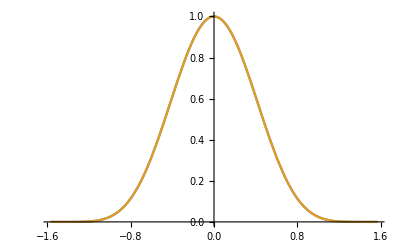

```mathematica
Plot[{Cos[phi]^6,Sin[phi-Pi/2]^6},{phi,-Pi/2,Pi/2}]
```

```mathematica
Series[(1-y*w)^(3/2),{y,0,4}]
```

1-(3 w y)/2+(3 w^2 y^2)/8+(w^3 y^3)/16+(3 w^4 y^4)/128+O[y]^5

```mathematica
Integrate[(1-w)^(v-1/2)/Sqrt[w]*(1-(3 w y)/2+(3 w^2 y^2)/8+(w^3 y^3)/16+(3 w^4 y^4)/128),{w,0,1}]
```

ConditionalExpression[1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y+576 (3+v) (4+v) y^2+240 (4+v) y^3+315 y^4) Gamma[1/2+v],Re[v]>-1/2]

```mathematica
FullSimplify[%]
```

ConditionalExpression[1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y+576 (3+v) (4+v) y^2+240 (4+v) y^3+315 y^4) Gamma[1/2+v],Re[v]>-1/2]

```mathematica
1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y+576 (3+v) (4+v) y^2+240 (4+v) y^3+315 y^4) Gamma[1/2+v] /. v -> 0
```

(π (49152-36864 y+6912 y^2+960 y^3+315 y^4))/49152

```mathematica
FullSimplify[%]
```

π (1-(3 y)/4+(y^2 (2304+5 y (64+21 y)))/16384)

```mathematica
1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y+576 (3+v) (4+v) y^2+240 (4+v) y^3+315 y^4) Gamma[1/2+v] /. v -> 1
```

(π (245760-92160 y+11520 y^2+1200 y^3+315 y^4))/491520

```mathematica
FullSimplify[%]
```

π/2+(π y (-6144+y (768+y (80+21 y))))/32768

```mathematica
1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y+576 (3+v) (4+v) y^2+240 (4+v) y^3+315 y^4) Gamma[1/2+v] /. v -> 2
```

(π (737280-184320 y+17280 y^2+1440 y^3+315 y^4))/1966080

```mathematica
FullSimplify[%]
```

(3 π)/8+(3 π y (-4096+y (384+y (32+7 y))))/131072

```mathematica
6144/32768
```

3/16

```mathematica
4096/131072
```

1/32

```mathematica
1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y+576 (3+v) (4+v) y^2+240 (4+v) y^3+315 y^4) Gamma[1/2+v] /. v -> 3
```

(π (1720320-322560 y+24192 y^2+1680 y^3+315 y^4))/5505024

```mathematica
1720320/5505024
```

5/16

```mathematica
322560/5505024
```

15/256

```mathematica
1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y)Gamma[1/2+v] /. v -> 2
```

(π (737280-184320 y))/1966080

```mathematica
FullSimplify[%]
```

-3/32 π (-4+y)

```mathematica
1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y)Gamma[1/2+v] /. v -> 4
```

(π (3440640-516096 y))/12582912

```mathematica
FullSimplify[%]
```

-7/512 π (-20+3 y)

```mathematica
1/(2048 Gamma[5+v])√π (2048 (1+v) (2+v) (3+v) (4+v)-1536 (2+v) (3+v) (4+v) y)Gamma[1/2+v] /. v -> 0
```

(π (49152-36864 y))/49152

```mathematica
FullSimplify[%]
```

π-(3 π y)/4

```mathematica
3/20*7/512
```

21/10240

```mathematica
10240/128
```

80

```mathematica
Integrate[(1-k2*w)^(1/2)*Sqrt[w]*(1-w)^(3/2),{w,0,1/k2}]
```

ConditionalExpression[(2 (-1+2 k2) (8+3 (-1+k2) k2) EllipticE[1/k2]-4 (-1+k2) (2+3 (-1+k2) k2) EllipticK[1/k2])/(105 k2^(5/2)),Re[k2]>1&&Im[k2]==0]

```mathematica
FullSimplify[%]
```

ConditionalExpression[(2 (-1+2 k2) (8+3 (-1+k2) k2) EllipticE[1/k2]-4 (-1+k2) (2+3 (-1+k2) k2) EllipticK[1/k2])/(105 k2^(5/2)),Re[k2]>1&&Im[k2]==0]

```mathematica
(9-1/k2)*2/15*(4-2*k2)+(k2-1)*2/3*(3-1/k2)
```

2/15 (9-1/k2) (4-2 k2)+2/3 (3-1/k2) (-1+k2)

```mathematica
Expand[%]
```

12/5+2/(15 k2)-(2 k2)/5

```mathematica
FullSimplify[%]
```

2/15 (18+1/k2-3 k2)

```mathematica
(4-2/k2)*2/15*(6-2/k2)+(k2-1)*2/3*(3-2/k2)
```

2/15 (4-2/k2) (6-2/k2)+2/3 (3-2/k2) (-1+k2)

```mathematica
FullSimplify[%]
```

2/15 (-1+4/k2^2-10/k2+15 k2)